```mathematica
g=0.1;
dMax=10;
dMin=1;
n=10;
δ=(dMax-dMin)/(n-1);
```

```mathematica
steps = Reap[Block[{dia},
For[i=0,i<10,i++,
dia=dMin + i * δ;
Sow[{i*0.5*(dia +(dMin)) + i*g, 10*dia}];
]]][[2,1]]
```

{{0.,10},{1.6,20},{4.2,30},{7.8,40},{12.4,50},{18.,60},{24.6,70},{32.2,80},{40.8,90},{50.4,100}}

```mathematica
fun=Table[{i*(dMin+g)+δ*0.5*i^2,10*(dMin+i*δ)},{i,0,n,0.1}];
```

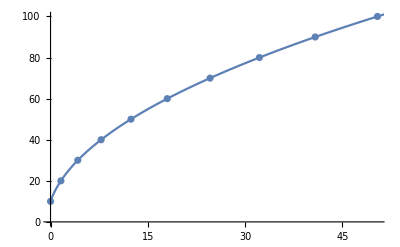

```mathematica
Show[ListPlot[steps],ListPlot[fun, Joined->True]]
```

```mathematica
Clear[g, dMin, δ,i]
```

```mathematica
Solve[i*(dMin+g)+δ*i^2/2==x,i]
```

{{i→(-dMin-g-√((dMin+g)^2+2 x δ))/δ},{i→(-dMin-g+√((dMin+g)^2+2 x δ))/δ}}

```mathematica
fun2=Table[{x,10*(dMin+δ*(-dMin-g+√((dMin+g)^2+2 x δ))/δ)},{x,0,50}];
```

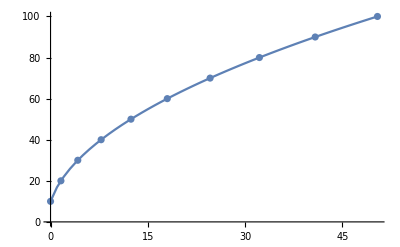

```mathematica
Show[ListPlot[steps],ListPlot[fun2, Joined->True]]
```